```mathematica
PrimeFV[n_]:=Module[{k,lines,f,i},
lines={{{1,1},{2,1}}};
For[k=2,k≤n,k++,
f=FactorInteger[k];
For[i=1,i<=Length[f],i++,
AppendTo[lines,{{k,PrimePi[f[[i,1]]]},{k+1,PrimePi[f[[i,1]]]}}];
];
];
Show[Graphics[Line[lines]]]
];
```

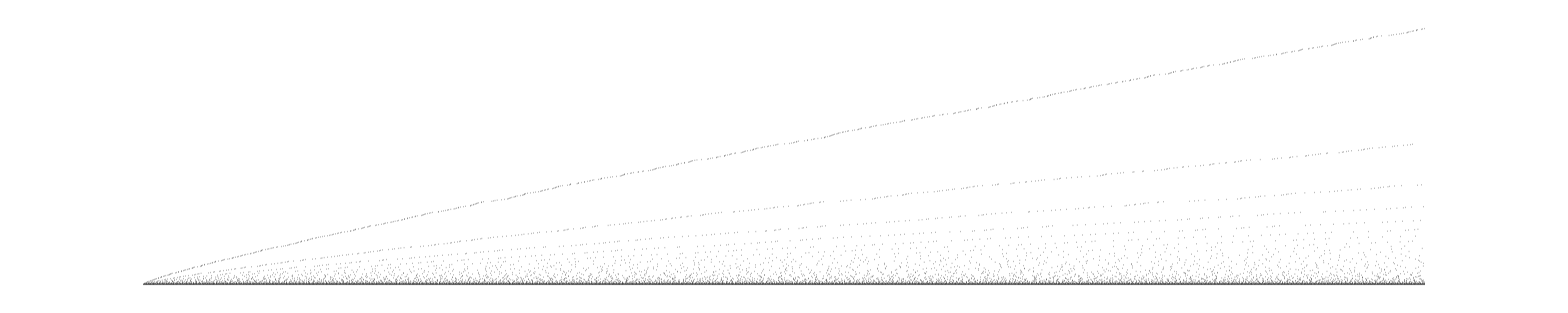

```mathematica
PrimeFV[5000]
```

```mathematica
Prime[3]
```

5

```mathematica
PrimePi[11]
```

5